FittedModel[-0.0146842+0.027567 x]

0.998439

{{θ→0.532673+36.2752 V}}

-90 | -2.482 | -2.521
-80 | -2.266 | -2.216
-70 | -1.905 | -1.87
-60 | -1.618 | -1.617
-50 | -1.351 | -1.358
-40 | -1.122 | -1.093
-30 | -0.874 | -0.885
-20 | -0.62 | -0.549
-10 | -0.297 | -0.299
0 | 0.012 | 0.019
10 | 0.302 | 0.221
20 | 0.547 | 0.49
30 | 0.699 | 0.755
40 | 0.998 | 1.022
50 | 1.265 | 1.289
60 | 1.58 | 1.569
70 | 1.954 | 1.945
80 | 2.28 | 2.248
90 | 2.59 | 2.6

FittedModel[0.124842+0.0290542 x]

{{θ→-4.29687+34.4184 V}}

0.988743

-90 | -2.61 | -2.57
-80 | -2.27 | -2.21
-70 | -1.98 | -1.89
-60 | -1.58 | -1.57
-50 | -1.34 | -1.37
-40 | -1.05 | -1.06
-30 | -0.82 | -0.81
-20 | -0.54 | -0.57
-10 | 0.24 | 0.25
0 | 0.5 | 0.7
10 | 0.37 | 0.32
20 | 0.62 | 0.58
30 | 0.86 | 0.85
40 | 1.21 | 1.12
50 | 1.47 | 1.39
60 | 1.82 | 1.7
70 | 2.16 | 2.18
80 | 2.51 | 2.44
90 | 2.91 | 2.78

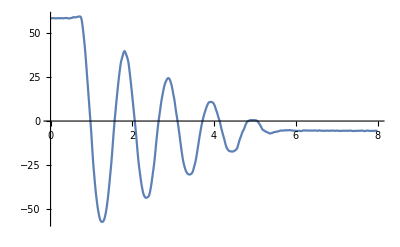

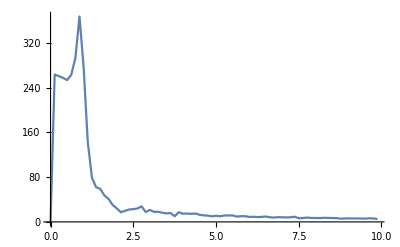

```mathematica
data={
{0,-2.482,-2.521},{10,-2.266,-2.216},{20,-1.905,-1.87},{30,-1.618,-1.617},{40,-1.351,-1.358},{50,-1.122,-1.093},{60,-0.874,-0.885},{70,-0.62,-0.549},{80,-0.297,-0.299},{90,0.012,0.019},{100,0.302,0.221},{110,0.547,0.49},{120,0.699,0.755},{130,0.998,1.022},{140,1.265,1.289},{150,1.58,1.569},{160,1.954,1.945},{170,2.28,2.248},{180,2.59,2.6}
};
data=SortBy[data, First];
data[[All,1]]=data[[All,1]]-90;

separated=Join[data[[All, {1, 2}]], data[[All, {1,3}]]];

angleModelUncond=LinearModelFit[separated, x, x]
angleModelUncond["AdjustedRSquared"]
inverseModelUncond=InverseFunction[angleModelUncond[#θ]&];
Solve[angleModelUncond[θ]==V, θ]//Expand

data[[All,{2, 3}]]=SetAccuracy[data[[All,{2, 3}]], 4];
Grid[data]

image=Show[
ListPlot[separated],
Plot[angleModelUncond[θ], {θ, Min[data[[All, 1]]], Max[data[[All, 1]]]}],
AxesLabel->{"Ângulo (°)", "Tensão elétrica (V)"}
];
Export[NotebookDirectory[]<>"/images/Pendulo-fit.pdf", image];

data={
{180,2.91,2.78},{170,2.51,2.44},{160,2.16,2.18},{150,1.82,1.7},{140,1.47,1.39},{130,1.21,1.12},{120,0.86,0.85},{110,0.622,0.582},{100,0.37,0.32},{90,0.5,0.7},{80,0.24,0.25},{70,-0.54,-0.57},{60,-0.82,-0.81},{50,-1.05,-1.06},{40,-1.34,-1.37},{30,-1.58,-1.57},{20,-1.98,-1.89},{10,-2.27,-2.21},{0,-2.61,-2.57}
};
data=SortBy[data, First];
data[[All,1]]=data[[All,1]]-90;

separated=Join[data[[All, {1, 2}]], data[[All, {1,3}]]];

angleModelCond=LinearModelFit[separated, x, x]
inverseModelCond=InverseFunction[angleModelCond[#θ]&];
Solve[angleModelCond[θ]==V, θ]//Expand
angleModelCond["RSquared"]

data[[All,{2, 3}]]=SetAccuracy[data[[All,{2, 3}]], 3];
Grid[data]

image=Show[
ListPlot[separated],
Plot[angleModelCond[θ], {θ, Min[data[[All, 1]]], Max[data[[All, 1]]]}],
AxesLabel->{"Ângulo (°)", "Tensão elétrica (V)"}
];
Export[NotebookDirectory[]<>"/images/Pendulo-Condicionado-fit.pdf", image];

data=Import[NotebookDirectory[]<>"../Data/Experimento7.lvm","TSV"];
data[[All,2]]=LowpassFilter[data[[All, 2]],40 / 250];
data[[All, 2]]=Map[inverseModelCond, data[[All, 2]]];

(* center on zero *)
(*data[[All,2]] = data[[All,2]]-Last[data[[All,2]]];*)
data[[All,2]] = data[[All,2]]-Mean[ data[[All,2]]];

Show[
ListLinePlot[data, ImageSize->Full, PlotRange->All],
Plot[90, {θ, Min[data[[All, 1]]], Max[data[[All, 1]]]}]
]

fourier=Table[{i, 0}, {i, 0, 250 , 250/(Length[data]-1)}];
fourier[[All, 2]]=Abs[Fourier[data[[All, 2]]]];

ListLinePlot[Take[fourier, 8*10], PlotRange->All]
```